```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
data = Import["solution.dat"];
sumenergy = Import["conserv_energy.dat"];
Length@data
```

1000

```mathematica
dataT=Partition[data,100];
dataXtemp=DeleteDuplicates[({#1[[1]],#1[[3]]}&/@#)&/@dataT];
dataTime =DeleteDuplicates[ #[[1,2]]&/@dataT];
sumenergy = Flatten@sumenergy;
TempMax =Max[Flatten@DeleteDuplicates[(#1[[3]]&/@#)&/@dataT]];
TempMin =Min[Flatten@DeleteDuplicates[(#1[[3]]&/@#)&/@dataT]];
```

```mathematica
(*ListPlot3D[data,ColorFunction->"TemperatureMap",PlotRange->Full,AxesLabel->{"x","t","T"}]*)
```

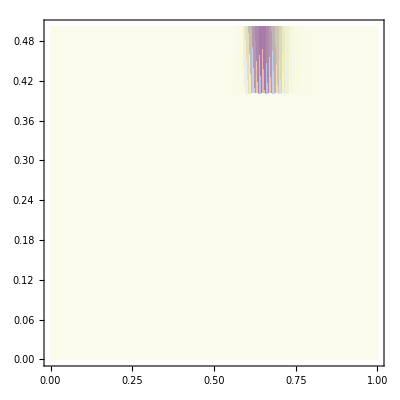

```mathematica
ListDensityPlot[data,ColorFunction->"TemperatureMap",PlotRange->All]
```

ListLinePlot::prng: Value of option PlotRange -> {{0,1},{Min[-6.73041×10^303,nan],Max[6.85967×10^303,nan]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

Part::partw: Part 8 of {{{0,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},«25»,{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},«50»},«5»,{«1»}} does not exist.

Part::partw: Part 8 of {{{0.,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},«25»,{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},«50»},«5»,{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{{0.,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},«25»,{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},«50»},«5»,{«1»}}⟦8⟧ is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: {{{0.,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},«25»,{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},«50»},«5»,{«1»}}⟦9⟧ is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: {{{0.,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},«25»,{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},«50»},«5»,{«1»}}⟦10⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

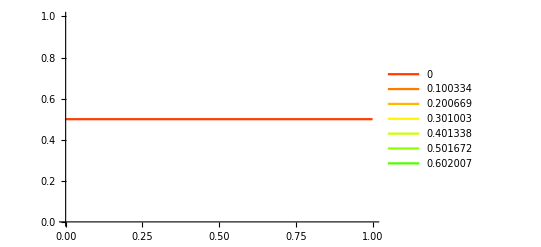
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListLinePlot[{{{0,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},{0.131313,0.5},{0.141414,0.5},{0.151515,0.5},{0.161616,0.5},{0.171717,0.5},{0.181818,0.5},{0.191919,0.5},{0.20202,0.5},{0.212121,0.5},{0.222222,0.5},{0.232323,0.5},{0.242424,0.5},{0.252525,0.5},{0.262626,0.5},{0.272727,0.5},{0.282828,0.5},{0.292929,0.5},{0.30303,0.5},{0.313131,0.5},{0.323232,0.5},{0.333333,0.5},{0.343434,0.5},{0.353535,0.5},{0.363636,0.5},{0.373737,0.5},{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},{0.505051,0.5},{0.515152,0.5},{0.525253,0.5},{0.535354,0.5},{0.545455,0.5},{0.555556,0.5},{0.565657,0.5},{0.575758,0.5},{0.585859,0.5},{0.59596,0.5},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.30984×10^56},{0.010101,-1.2667×10^56},{0.020202,1.14554×10^56},{0.030303,-9.68557×10^55},{0.040404,7.65326×10^55},{0.0505051,-5.64845×10^55},{0.0606061,3.89095×10^55},{0.0707071,-2.49934×10^55},{0.0808081,1.49538×10^55},{0.0909091,-8.3225×10^54},{0.10101,4.30177×10^54},{0.111111,-2.06125×10^54},{0.121212,9.13635×10^53},{0.131313,-3.7367×10^53},{0.141414,1.40611×10^53},{0.151515,-4.85176×10^52},{0.161616,1.52905×10^52},{0.171717,-4.38106×10^51},{0.181818,1.13501×10^51},{0.191919,-2.64152×10^50},{0.20202,5.47931×10^49},{0.212121,-1.00331×10^49},{0.222222,1.60236×10^48},{0.232323,-2.198×10^47},{0.242424,2.53772×10^46},{0.252525,-2.39847×10^45},{0.262626,1.78203×10^44},{0.272727,-9.76121×10^42},{0.282828,3.505×10^41},{0.292929,-6.18961×10^39},{0.30303,0.5},{0.313131,0.5},{0.323232,0.5},{0.333333,0.5},{0.343434,0.5},{0.353535,0.5},{0.363636,0.5},{0.373737,0.5},{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},{0.505051,0.5},{0.515152,0.5},{0.525253,0.5},{0.535354,0.5},{0.545455,0.5},{0.555556,0.5},{0.565657,0.5},{0.575758,0.5},{0.585859,0.5},{0.59596,0.5},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.15116×10^114},{0.010101,-1.1322×10^114},{0.020202,1.07716×10^114},{0.030303,-9.91276×10^113},{0.040404,8.82361×10^113},{0.0505051,-7.59637×10^113},{0.0606061,6.32465×10^113},{0.0707071,-5.09203×10^113},{0.0808081,3.96383×10^113},{0.0909091,-2.98294×10^113},{0.10101,2.16973×10^113},{0.111111,-1.52517×10^113},{0.121212,1.03583×10^113},{0.131313,-6.79535×10^112},{0.141414,4.30506×10^112},{0.151515,-2.63309×10^112},{0.161616,1.5543×10^112},{0.171717,-8.85202×10^111},{0.181818,4.86212×10^111},{0.191919,-2.57462×10^111},{0.20202,1.31377×10^111},{0.212121,-6.4571×10^110},{0.222222,3.0553×10^110},{0.232323,-1.39102×10^110},{0.242424,6.09009×10^109},{0.252525,-2.56243×10^109},{0.262626,1.03544×10^109},{0.272727,-4.01539×10^108},{0.282828,1.4932×10^108},{0.292929,-5.32027×10^107},{0.30303,1.81457×10^107},{0.313131,-5.91852×10^106},{0.323232,1.84411×10^106},{0.333333,-5.48272×10^105},{0.343434,1.55344×10^105},{0.353535,-4.18879×10^104},{0.363636,1.07333×10^104},{0.373737,-2.60928×10^103},{0.383838,6.0073×10^102},{0.393939,-1.30724×10^102},{0.40404,2.68292×10^101},{0.414141,-5.18078×10^100},{0.424242,9.38762×10^99},{0.434343,-1.59144×10^99},{0.444444,2.51555×10^98},{0.454545,-3.69342×10^97},{0.464646,5.01512×10^96},{0.474747,-6.26628×10^95},{0.484848,7.16267×10^94},{0.494949,-7.43904×10^93},{0.505051,7.03137×10^92},{0.515152,-6.67592×10^91},{0.525253,6.73331×10^90},{0.535354,-6.83893×10^89},{0.545455,6.64547×10^88},{0.555556,-5.85758×10^87},{0.565657,4.40525×10^86},{0.575758,-2.60668×10^85},{0.585859,1.06454×10^84},{0.59596,-2.22674×10^82},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.17307×10^172},{0.010101,-1.16019×10^172},{0.020202,1.12238×10^172},{0.030303,-1.06208×10^172},{0.040404,9.83035×10^171},{0.0505051,-8.8996×10^171},{0.0606061,7.88044×10^171},{0.0707071,-6.82489×10^171},{0.0808081,5.78081×10^171},{0.0909091,-4.78865×10^171},{0.10101,3.87924×10^171},{0.111111,-3.07302×10^171},{0.121212,2.38037×10^171},{0.131313,-1.80283×10^171},{0.141414,1.33494×10^171},{0.151515,-9.66357×10^170},{0.161616,6.83817×10^170},{0.171717,-4.72967×10^170},{0.181818,3.19718×10^170},{0.191919,-2.11204×10^170},{0.20202,1.36329×10^170},{0.212121,-8.59753×10^169},{0.222222,5.29666×10^169},{0.232323,-3.18724×10^169},{0.242424,1.87305×10^169},{0.252525,-1.07484×10^169},{0.262626,6.02173×10^168},{0.272727,-3.29318×10^168},{0.282828,1.75771×10^168},{0.292929,-9.15446×10^167},{0.30303,4.65147×10^167},{0.313131,-2.3053×10^167},{0.323232,1.11417×10^167},{0.333333,-5.25003×10^166},{0.343434,2.41131×10^166},{0.353535,-1.07924×10^166},{0.363636,4.70586×10^165},{0.373737,-1.99846×10^165},{0.383838,8.26344×10^164},{0.393939,-3.32584×10^164},{0.40404,1.30249×10^164},{0.414141,-4.96177×10^163},{0.424242,1.83793×10^163},{0.434343,-6.61746×10^162},{0.444444,2.31499×10^162},{0.454545,-7.86544×10^161},{0.464646,2.59432×10^161},{0.474747,-8.30353×10^160},{0.484848,2.57858×10^160},{0.494949,-7.8018×10^159},{0.505051,2.44098×10^159},{0.515152,-9.77055×10^158},{0.525253,5.88413×10^158},{0.535354,-5.30616×10^158},{0.545455,6.48789×10^158},{0.555556,-9.29949×10^158},{0.565657,1.3964×10^159},{0.575758,-2.05089×10^159},{0.585859,2.81431×10^159},{0.59596,-3.45719×10^159},{0.606061,3.58445×10^159},{0.616162,-3.04646×10^159},{0.626263,2.17456×10^159},{0.636364,-1.35056×10^159},{0.646465,7.43982×10^158},{0.656566,-3.67787×10^158},{0.666667,1.64406×10^158},{0.676768,-6.67937×10^157},{0.686869,2.47468×10^157},{0.69697,-8.37924×10^156},{0.707071,2.59605×10^156},{0.717172,-7.36234×10^155},{0.727273,1.91066×10^155},{0.737374,-4.53313×10^154},{0.747475,9.81669×10^153},{0.757576,-1.93596×10^153},{0.767677,3.46651×10^152},{0.777778,-5.61434×10^151},{0.787879,8.18561×10^150},{0.79798,-1.06804×10^150},{0.808081,1.23802×10^149},{0.818182,-1.26326×10^148},{0.828283,1.12162×10^147},{0.838384,-8.53638×10^145},{0.848485,5.4592×10^144},{0.858586,-2.85403×10^143},{0.868687,1.17165×10^142},{0.878788,-3.54293×10^140},{0.888889,7.01833×10^138},{0.89899,-6.83418×10^136},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.26922×10^230},{0.010101,-1.25877×10^230},{0.020202,1.22792×10^230},{0.030303,-1.17817×10^230},{0.040404,1.11187×10^230},{0.0505051,-1.03208×10^230},{0.0606061,9.42263×10^229},{0.0707071,-8.46115×10^229},{0.0808081,7.4727×10^229},{0.0909091,-6.49097×10^229},{0.10101,5.54518×10^229},{0.111111,-4.65893×10^229},{0.121212,3.84956×10^229},{0.131313,-3.12808×10^229},{0.141414,2.49962×10^229},{0.151515,-1.96419×10^229},{0.161616,1.51773×10^229},{0.171717,-1.15316×10^229},{0.181818,8.61485×10^228},{0.191919,-6.32783×10^228},{0.20202,4.56971×10^228},{0.212121,-3.24437×10^228},{0.222222,2.26441×10^228},{0.232323,-1.55361×10^228},{0.242424,1.04777×10^228},{0.252525,-6.94541×10^227},{0.262626,4.52496×10^227},{0.272727,-2.89725×10^227},{0.282828,1.82299×10^227},{0.292929,-1.12713×10^227},{0.30303,6.84741×10^226},{0.313131,-4.08701×10^226},{0.323232,2.39649×10^226},{0.333333,-1.38039×10^226},{0.343434,7.80987×10^225},{0.353535,-4.33972×10^225},{0.363636,2.36818×10^225},{0.373737,-1.26899×10^225},{0.383838,6.67644×10^224},{0.393939,-3.44851×10^224},{0.40404,1.74851×10^224},{0.414141,-8.7017×10^223},{0.424242,4.25×10^223},{0.434343,-2.03704×10^223},{0.444444,9.59311×10^222},{0.454545,-4.5501×10^222},{0.464646,3.15714×10^222},{0.474747,-1.11733×10^223},{0.484848,9.25762×10^223},{0.494949,-8.32588×10^224},{0.505051,7.564×10^225},{0.515152,-6.20723×10^226},{0.525253,4.16894×10^227},{0.535354,-2.30668×10^228},{0.545455,1.06519×10^229},{0.555556,-4.1383×10^229},{0.565657,1.35752×10^230},{0.575758,-3.75721×10^230},{0.585859,8.72136×10^230},{0.59596,-1.67514×10^231},{0.606061,2.59232×10^231},{0.616162,-3.28349×10^231},{0.626263,3.59076×10^231},{0.636364,-3.54236×10^231},{0.646465,3.21887×10^231},{0.656566,-2.72572×10^231},{0.666667,2.16663×10^231},{0.676768,-1.62454×10^231},{0.686869,1.15298×10^231},{0.69697,-7.76538×10^230},{0.707071,4.97276×10^230},{0.717172,-3.03235×10^230},{0.727273,1.76288×10^230},{0.737374,-9.77992×10^229},{0.747475,5.18134×10^229},{0.757576,-2.62299×10^229},{0.767677,1.2694×10^229},{0.777778,-5.87475×10^228},{0.787879,2.60062×10^228},{0.79798,-1.10135×10^228},{0.808081,4.46227×10^227},{0.818182,-1.72969×10^227},{0.828283,6.41383×10^226},{0.838384,-2.27476×10^226},{0.848485,7.71475×10^225},{0.858586,-2.50115×10^225},{0.868687,7.7487×10^224},{0.878788,-2.29294×10^224},{0.888889,6.4774×10^223},{0.89899,-1.74579×10^223},{0.909091,4.4861×10^222},{0.919192,-1.09823×10^222},{0.929293,2.55913×10^221},{0.939394,-5.67073×10^220},{0.949495,1.19362×10^220},{0.959596,-2.38372×10^219},{0.969697,4.51045×10^218},{0.979798,-8.07024×10^217},{0.989899,1.33277×10^217},{1,0.5}},{{0,1.41887×10^288},{0.010101,-1.40952×10^288},{0.020202,1.38184×10^288},{0.030303,-1.3369×10^288},{0.040404,1.27643×10^288},{0.0505051,-1.20267×10^288},{0.0606061,1.11828×10^288},{0.0707071,-1.02612×10^288},{0.0808081,9.29163×10^287},{0.0909091,-8.30283×10^287},{0.10101,7.32145×10^287},{0.111111,-6.37088×10^287},{0.121212,5.4705×10^287},{0.131313,-4.63527×10^287},{0.141414,3.87557×10^287},{0.151515,-3.19744×10^287},{0.161616,2.60296×10^287},{0.171717,-2.09085×10^287},{0.181818,1.65714×10^287},{0.191919,-1.29589×10^287},{0.20202,9.99854×10^286},{0.212121,-7.6113×10^286},{0.222222,5.71638×10^286},{0.232323,-4.23557×10^286},{0.242424,3.09613×10^286},{0.252525,-2.2327×10^286},{0.262626,1.5883×10^286},{0.272727,-1.11458×10^286},{0.282828,7.71526×10^285},{0.292929,-5.26788×10^285},{0.30303,3.54774×10^285},{0.313131,-2.35658×10^285},{0.323232,1.54388×10^285},{0.333333,-9.97677×10^284},{0.343434,6.37249×10^284},{0.353535,-4.14941×10^284},{0.363636,3.93784×10^284},{0.373737,-1.52937×10^285},{0.383838,1.30948×10^286},{0.393939,-1.2295×10^287},{0.40404,1.16326×10^288},{0.414141,-1.10257×10^289},{0.424242,1.04645×10^290},{0.434343,-9.94418×10^290},{0.444444,9.46067×10^291},{0.454545,-9.01049×10^292},{0.464646,8.59057×10^293},{0.474747,-8.19819×10^294},{0.484848,7.83093×10^295},{0.494949,-7.48666×10^296},{0.505051,7.16346×10^297},{0.515152,-6.16458×10^298},{0.525253,4.33145×10^299},{0.535354,-2.50414×10^300},{0.545455,1.20719×10^301},{0.555556,-4.89362×10^301},{0.565657,1.67491×10^302},{0.575758,-4.83938×10^302},{0.585859,1.17442×10^303},{0.59596,-2.3654×10^303},{0.606061,3.86149×10^303},{0.616162,-5.21919×10^303},{0.626263,6.18742×10^303},{0.636364,-6.73041×10^303},{0.646465,6.85967×10^303},{0.656566,-6.62655×10^303},{0.666667,6.10992×10^303},{0.676768,-5.40185×10^303},{0.686869,4.59399×10^303},{0.69697,-3.76685×10^303},{0.707071,2.98298×10^303},{0.717172,-2.28445×10^303},{0.727273,1.69363×10^303},{0.737374,-1.21651×10^303},{0.747475,8.47166×10^302},{0.757576,-5.72278×10^302},{0.767677,3.75168×10^302},{0.777778,-2.38774×10^302},{0.787879,1.47577×10^302},{0.79798,-8.86004×10^301},{0.808081,5.16801×10^301},{0.818182,-2.92924×10^301},{0.828283,1.61357×10^301},{0.838384,-8.63904×10^300},{0.848485,4.49596×10^300},{0.858586,-2.27446×10^300},{0.868687,1.11852×10^300},{0.878788,-5.34717×10^299},{0.888889,2.4849×10^299},{0.89899,-1.12249×10^299},{0.909091,4.92861×10^298},{0.919192,-2.1033×10^298},{0.929293,8.72311×10^297},{0.939394,-3.51552×10^297},{0.949495,1.37656×10^297},{0.959596,-5.23572×10^296},{0.969697,1.93219×10^296},{0.979798,-6.85711×10^295},{0.989899,2.15029×10^295},{1,0.5}},{{0,nan},{0.010101,nan},{0.020202,nan},{0.030303,nan},{0.040404,nan},{0.0505051,nan},{0.0606061,nan},{0.0707071,nan},{0.0808081,nan},{0.0909091,nan},{0.10101,nan},{0.111111,nan},{0.121212,nan},{0.131313,nan},{0.141414,nan},{0.151515,nan},{0.161616,nan},{0.171717,nan},{0.181818,nan},{0.191919,nan},{0.20202,nan},{0.212121,nan},{0.222222,nan},{0.232323,nan},{0.242424,nan},{0.252525,nan},{0.262626,nan},{0.272727,nan},{0.282828,nan},{0.292929,nan},{0.30303,nan},{0.313131,nan},{0.323232,nan},{0.333333,nan},{0.343434,nan},{0.353535,nan},{0.363636,nan},{0.373737,nan},{0.383838,nan},{0.393939,nan},{0.40404,nan},{0.414141,nan},{0.424242,nan},{0.434343,nan},{0.444444,nan},{0.454545,nan},{0.464646,nan},{0.474747,nan},{0.484848,nan},{0.494949,nan},{0.505051,nan},{0.515152,nan},{0.525253,nan},{0.535354,nan},{0.545455,nan},{0.555556,nan},{0.565657,nan},{0.575758,nan},{0.585859,nan},{0.59596,nan},{0.606061,nan},{0.616162,nan},{0.626263,nan},{0.636364,nan},{0.646465,nan},{0.656566,nan},{0.666667,nan},{0.676768,nan},{0.686869,nan},{0.69697,nan},{0.707071,nan},{0.717172,nan},{0.727273,nan},{0.737374,nan},{0.747475,nan},{0.757576,nan},{0.767677,nan},{0.777778,nan},{0.787879,nan},{0.79798,nan},{0.808081,nan},{0.818182,nan},{0.828283,nan},{0.838384,nan},{0.848485,nan},{0.858586,nan},{0.868687,nan},{0.878788,nan},{0.888889,nan},{0.89899,nan},{0.909091,nan},{0.919192,nan},{0.929293,nan},{0.939394,nan},{0.949495,nan},{0.959596,nan},{0.969697,nan},{0.979798,nan},{0.989899,nan},{1,nan}}}⟦8⟧,PlotRange→{{0,1},{Min[-6.73041×10^303,nan],Max[6.85967×10^303,nan]}},PlotStyle→{Hue[Rational[8, 25]]},PlotLegends→{0.702341}],ListLinePlot[{{{0,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},{0.131313,0.5},{0.141414,0.5},{0.151515,0.5},{0.161616,0.5},{0.171717,0.5},{0.181818,0.5},{0.191919,0.5},{0.20202,0.5},{0.212121,0.5},{0.222222,0.5},{0.232323,0.5},{0.242424,0.5},{0.252525,0.5},{0.262626,0.5},{0.272727,0.5},{0.282828,0.5},{0.292929,0.5},{0.30303,0.5},{0.313131,0.5},{0.323232,0.5},{0.333333,0.5},{0.343434,0.5},{0.353535,0.5},{0.363636,0.5},{0.373737,0.5},{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},{0.505051,0.5},{0.515152,0.5},{0.525253,0.5},{0.535354,0.5},{0.545455,0.5},{0.555556,0.5},{0.565657,0.5},{0.575758,0.5},{0.585859,0.5},{0.59596,0.5},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.30984×10^56},{0.010101,-1.2667×10^56},{0.020202,1.14554×10^56},{0.030303,-9.68557×10^55},{0.040404,7.65326×10^55},{0.0505051,-5.64845×10^55},{0.0606061,3.89095×10^55},{0.0707071,-2.49934×10^55},{0.0808081,1.49538×10^55},{0.0909091,-8.3225×10^54},{0.10101,4.30177×10^54},{0.111111,-2.06125×10^54},{0.121212,9.13635×10^53},{0.131313,-3.7367×10^53},{0.141414,1.40611×10^53},{0.151515,-4.85176×10^52},{0.161616,1.52905×10^52},{0.171717,-4.38106×10^51},{0.181818,1.13501×10^51},{0.191919,-2.64152×10^50},{0.20202,5.47931×10^49},{0.212121,-1.00331×10^49},{0.222222,1.60236×10^48},{0.232323,-2.198×10^47},{0.242424,2.53772×10^46},{0.252525,-2.39847×10^45},{0.262626,1.78203×10^44},{0.272727,-9.76121×10^42},{0.282828,3.505×10^41},{0.292929,-6.18961×10^39},{0.30303,0.5},{0.313131,0.5},{0.323232,0.5},{0.333333,0.5},{0.343434,0.5},{0.353535,0.5},{0.363636,0.5},{0.373737,0.5},{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},{0.505051,0.5},{0.515152,0.5},{0.525253,0.5},{0.535354,0.5},{0.545455,0.5},{0.555556,0.5},{0.565657,0.5},{0.575758,0.5},{0.585859,0.5},{0.59596,0.5},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.15116×10^114},{0.010101,-1.1322×10^114},{0.020202,1.07716×10^114},{0.030303,-9.91276×10^113},{0.040404,8.82361×10^113},{0.0505051,-7.59637×10^113},{0.0606061,6.32465×10^113},{0.0707071,-5.09203×10^113},{0.0808081,3.96383×10^113},{0.0909091,-2.98294×10^113},{0.10101,2.16973×10^113},{0.111111,-1.52517×10^113},{0.121212,1.03583×10^113},{0.131313,-6.79535×10^112},{0.141414,4.30506×10^112},{0.151515,-2.63309×10^112},{0.161616,1.5543×10^112},{0.171717,-8.85202×10^111},{0.181818,4.86212×10^111},{0.191919,-2.57462×10^111},{0.20202,1.31377×10^111},{0.212121,-6.4571×10^110},{0.222222,3.0553×10^110},{0.232323,-1.39102×10^110},{0.242424,6.09009×10^109},{0.252525,-2.56243×10^109},{0.262626,1.03544×10^109},{0.272727,-4.01539×10^108},{0.282828,1.4932×10^108},{0.292929,-5.32027×10^107},{0.30303,1.81457×10^107},{0.313131,-5.91852×10^106},{0.323232,1.84411×10^106},{0.333333,-5.48272×10^105},{0.343434,1.55344×10^105},{0.353535,-4.18879×10^104},{0.363636,1.07333×10^104},{0.373737,-2.60928×10^103},{0.383838,6.0073×10^102},{0.393939,-1.30724×10^102},{0.40404,2.68292×10^101},{0.414141,-5.18078×10^100},{0.424242,9.38762×10^99},{0.434343,-1.59144×10^99},{0.444444,2.51555×10^98},{0.454545,-3.69342×10^97},{0.464646,5.01512×10^96},{0.474747,-6.26628×10^95},{0.484848,7.16267×10^94},{0.494949,-7.43904×10^93},{0.505051,7.03137×10^92},{0.515152,-6.67592×10^91},{0.525253,6.73331×10^90},{0.535354,-6.83893×10^89},{0.545455,6.64547×10^88},{0.555556,-5.85758×10^87},{0.565657,4.40525×10^86},{0.575758,-2.60668×10^85},{0.585859,1.06454×10^84},{0.59596,-2.22674×10^82},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.17307×10^172},{0.010101,-1.16019×10^172},{0.020202,1.12238×10^172},{0.030303,-1.06208×10^172},{0.040404,9.83035×10^171},{0.0505051,-8.8996×10^171},{0.0606061,7.88044×10^171},{0.0707071,-6.82489×10^171},{0.0808081,5.78081×10^171},{0.0909091,-4.78865×10^171},{0.10101,3.87924×10^171},{0.111111,-3.07302×10^171},{0.121212,2.38037×10^171},{0.131313,-1.80283×10^171},{0.141414,1.33494×10^171},{0.151515,-9.66357×10^170},{0.161616,6.83817×10^170},{0.171717,-4.72967×10^170},{0.181818,3.19718×10^170},{0.191919,-2.11204×10^170},{0.20202,1.36329×10^170},{0.212121,-8.59753×10^169},{0.222222,5.29666×10^169},{0.232323,-3.18724×10^169},{0.242424,1.87305×10^169},{0.252525,-1.07484×10^169},{0.262626,6.02173×10^168},{0.272727,-3.29318×10^168},{0.282828,1.75771×10^168},{0.292929,-9.15446×10^167},{0.30303,4.65147×10^167},{0.313131,-2.3053×10^167},{0.323232,1.11417×10^167},{0.333333,-5.25003×10^166},{0.343434,2.41131×10^166},{0.353535,-1.07924×10^166},{0.363636,4.70586×10^165},{0.373737,-1.99846×10^165},{0.383838,8.26344×10^164},{0.393939,-3.32584×10^164},{0.40404,1.30249×10^164},{0.414141,-4.96177×10^163},{0.424242,1.83793×10^163},{0.434343,-6.61746×10^162},{0.444444,2.31499×10^162},{0.454545,-7.86544×10^161},{0.464646,2.59432×10^161},{0.474747,-8.30353×10^160},{0.484848,2.57858×10^160},{0.494949,-7.8018×10^159},{0.505051,2.44098×10^159},{0.515152,-9.77055×10^158},{0.525253,5.88413×10^158},{0.535354,-5.30616×10^158},{0.545455,6.48789×10^158},{0.555556,-9.29949×10^158},{0.565657,1.3964×10^159},{0.575758,-2.05089×10^159},{0.585859,2.81431×10^159},{0.59596,-3.45719×10^159},{0.606061,3.58445×10^159},{0.616162,-3.04646×10^159},{0.626263,2.17456×10^159},{0.636364,-1.35056×10^159},{0.646465,7.43982×10^158},{0.656566,-3.67787×10^158},{0.666667,1.64406×10^158},{0.676768,-6.67937×10^157},{0.686869,2.47468×10^157},{0.69697,-8.37924×10^156},{0.707071,2.59605×10^156},{0.717172,-7.36234×10^155},{0.727273,1.91066×10^155},{0.737374,-4.53313×10^154},{0.747475,9.81669×10^153},{0.757576,-1.93596×10^153},{0.767677,3.46651×10^152},{0.777778,-5.61434×10^151},{0.787879,8.18561×10^150},{0.79798,-1.06804×10^150},{0.808081,1.23802×10^149},{0.818182,-1.26326×10^148},{0.828283,1.12162×10^147},{0.838384,-8.53638×10^145},{0.848485,5.4592×10^144},{0.858586,-2.85403×10^143},{0.868687,1.17165×10^142},{0.878788,-3.54293×10^140},{0.888889,7.01833×10^138},{0.89899,-6.83418×10^136},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.26922×10^230},{0.010101,-1.25877×10^230},{0.020202,1.22792×10^230},{0.030303,-1.17817×10^230},{0.040404,1.11187×10^230},{0.0505051,-1.03208×10^230},{0.0606061,9.42263×10^229},{0.0707071,-8.46115×10^229},{0.0808081,7.4727×10^229},{0.0909091,-6.49097×10^229},{0.10101,5.54518×10^229},{0.111111,-4.65893×10^229},{0.121212,3.84956×10^229},{0.131313,-3.12808×10^229},{0.141414,2.49962×10^229},{0.151515,-1.96419×10^229},{0.161616,1.51773×10^229},{0.171717,-1.15316×10^229},{0.181818,8.61485×10^228},{0.191919,-6.32783×10^228},{0.20202,4.56971×10^228},{0.212121,-3.24437×10^228},{0.222222,2.26441×10^228},{0.232323,-1.55361×10^228},{0.242424,1.04777×10^228},{0.252525,-6.94541×10^227},{0.262626,4.52496×10^227},{0.272727,-2.89725×10^227},{0.282828,1.82299×10^227},{0.292929,-1.12713×10^227},{0.30303,6.84741×10^226},{0.313131,-4.08701×10^226},{0.323232,2.39649×10^226},{0.333333,-1.38039×10^226},{0.343434,7.80987×10^225},{0.353535,-4.33972×10^225},{0.363636,2.36818×10^225},{0.373737,-1.26899×10^225},{0.383838,6.67644×10^224},{0.393939,-3.44851×10^224},{0.40404,1.74851×10^224},{0.414141,-8.7017×10^223},{0.424242,4.25×10^223},{0.434343,-2.03704×10^223},{0.444444,9.59311×10^222},{0.454545,-4.5501×10^222},{0.464646,3.15714×10^222},{0.474747,-1.11733×10^223},{0.484848,9.25762×10^223},{0.494949,-8.32588×10^224},{0.505051,7.564×10^225},{0.515152,-6.20723×10^226},{0.525253,4.16894×10^227},{0.535354,-2.30668×10^228},{0.545455,1.06519×10^229},{0.555556,-4.1383×10^229},{0.565657,1.35752×10^230},{0.575758,-3.75721×10^230},{0.585859,8.72136×10^230},{0.59596,-1.67514×10^231},{0.606061,2.59232×10^231},{0.616162,-3.28349×10^231},{0.626263,3.59076×10^231},{0.636364,-3.54236×10^231},{0.646465,3.21887×10^231},{0.656566,-2.72572×10^231},{0.666667,2.16663×10^231},{0.676768,-1.62454×10^231},{0.686869,1.15298×10^231},{0.69697,-7.76538×10^230},{0.707071,4.97276×10^230},{0.717172,-3.03235×10^230},{0.727273,1.76288×10^230},{0.737374,-9.77992×10^229},{0.747475,5.18134×10^229},{0.757576,-2.62299×10^229},{0.767677,1.2694×10^229},{0.777778,-5.87475×10^228},{0.787879,2.60062×10^228},{0.79798,-1.10135×10^228},{0.808081,4.46227×10^227},{0.818182,-1.72969×10^227},{0.828283,6.41383×10^226},{0.838384,-2.27476×10^226},{0.848485,7.71475×10^225},{0.858586,-2.50115×10^225},{0.868687,7.7487×10^224},{0.878788,-2.29294×10^224},{0.888889,6.4774×10^223},{0.89899,-1.74579×10^223},{0.909091,4.4861×10^222},{0.919192,-1.09823×10^222},{0.929293,2.55913×10^221},{0.939394,-5.67073×10^220},{0.949495,1.19362×10^220},{0.959596,-2.38372×10^219},{0.969697,4.51045×10^218},{0.979798,-8.07024×10^217},{0.989899,1.33277×10^217},{1,0.5}},{{0,1.41887×10^288},{0.010101,-1.40952×10^288},{0.020202,1.38184×10^288},{0.030303,-1.3369×10^288},{0.040404,1.27643×10^288},{0.0505051,-1.20267×10^288},{0.0606061,1.11828×10^288},{0.0707071,-1.02612×10^288},{0.0808081,9.29163×10^287},{0.0909091,-8.30283×10^287},{0.10101,7.32145×10^287},{0.111111,-6.37088×10^287},{0.121212,5.4705×10^287},{0.131313,-4.63527×10^287},{0.141414,3.87557×10^287},{0.151515,-3.19744×10^287},{0.161616,2.60296×10^287},{0.171717,-2.09085×10^287},{0.181818,1.65714×10^287},{0.191919,-1.29589×10^287},{0.20202,9.99854×10^286},{0.212121,-7.6113×10^286},{0.222222,5.71638×10^286},{0.232323,-4.23557×10^286},{0.242424,3.09613×10^286},{0.252525,-2.2327×10^286},{0.262626,1.5883×10^286},{0.272727,-1.11458×10^286},{0.282828,7.71526×10^285},{0.292929,-5.26788×10^285},{0.30303,3.54774×10^285},{0.313131,-2.35658×10^285},{0.323232,1.54388×10^285},{0.333333,-9.97677×10^284},{0.343434,6.37249×10^284},{0.353535,-4.14941×10^284},{0.363636,3.93784×10^284},{0.373737,-1.52937×10^285},{0.383838,1.30948×10^286},{0.393939,-1.2295×10^287},{0.40404,1.16326×10^288},{0.414141,-1.10257×10^289},{0.424242,1.04645×10^290},{0.434343,-9.94418×10^290},{0.444444,9.46067×10^291},{0.454545,-9.01049×10^292},{0.464646,8.59057×10^293},{0.474747,-8.19819×10^294},{0.484848,7.83093×10^295},{0.494949,-7.48666×10^296},{0.505051,7.16346×10^297},{0.515152,-6.16458×10^298},{0.525253,4.33145×10^299},{0.535354,-2.50414×10^300},{0.545455,1.20719×10^301},{0.555556,-4.89362×10^301},{0.565657,1.67491×10^302},{0.575758,-4.83938×10^302},{0.585859,1.17442×10^303},{0.59596,-2.3654×10^303},{0.606061,3.86149×10^303},{0.616162,-5.21919×10^303},{0.626263,6.18742×10^303},{0.636364,-6.73041×10^303},{0.646465,6.85967×10^303},{0.656566,-6.62655×10^303},{0.666667,6.10992×10^303},{0.676768,-5.40185×10^303},{0.686869,4.59399×10^303},{0.69697,-3.76685×10^303},{0.707071,2.98298×10^303},{0.717172,-2.28445×10^303},{0.727273,1.69363×10^303},{0.737374,-1.21651×10^303},{0.747475,8.47166×10^302},{0.757576,-5.72278×10^302},{0.767677,3.75168×10^302},{0.777778,-2.38774×10^302},{0.787879,1.47577×10^302},{0.79798,-8.86004×10^301},{0.808081,5.16801×10^301},{0.818182,-2.92924×10^301},{0.828283,1.61357×10^301},{0.838384,-8.63904×10^300},{0.848485,4.49596×10^300},{0.858586,-2.27446×10^300},{0.868687,1.11852×10^300},{0.878788,-5.34717×10^299},{0.888889,2.4849×10^299},{0.89899,-1.12249×10^299},{0.909091,4.92861×10^298},{0.919192,-2.1033×10^298},{0.929293,8.72311×10^297},{0.939394,-3.51552×10^297},{0.949495,1.37656×10^297},{0.959596,-5.23572×10^296},{0.969697,1.93219×10^296},{0.979798,-6.85711×10^295},{0.989899,2.15029×10^295},{1,0.5}},{{0,nan},{0.010101,nan},{0.020202,nan},{0.030303,nan},{0.040404,nan},{0.0505051,nan},{0.0606061,nan},{0.0707071,nan},{0.0808081,nan},{0.0909091,nan},{0.10101,nan},{0.111111,nan},{0.121212,nan},{0.131313,nan},{0.141414,nan},{0.151515,nan},{0.161616,nan},{0.171717,nan},{0.181818,nan},{0.191919,nan},{0.20202,nan},{0.212121,nan},{0.222222,nan},{0.232323,nan},{0.242424,nan},{0.252525,nan},{0.262626,nan},{0.272727,nan},{0.282828,nan},{0.292929,nan},{0.30303,nan},{0.313131,nan},{0.323232,nan},{0.333333,nan},{0.343434,nan},{0.353535,nan},{0.363636,nan},{0.373737,nan},{0.383838,nan},{0.393939,nan},{0.40404,nan},{0.414141,nan},{0.424242,nan},{0.434343,nan},{0.444444,nan},{0.454545,nan},{0.464646,nan},{0.474747,nan},{0.484848,nan},{0.494949,nan},{0.505051,nan},{0.515152,nan},{0.525253,nan},{0.535354,nan},{0.545455,nan},{0.555556,nan},{0.565657,nan},{0.575758,nan},{0.585859,nan},{0.59596,nan},{0.606061,nan},{0.616162,nan},{0.626263,nan},{0.636364,nan},{0.646465,nan},{0.656566,nan},{0.666667,nan},{0.676768,nan},{0.686869,nan},{0.69697,nan},{0.707071,nan},{0.717172,nan},{0.727273,nan},{0.737374,nan},{0.747475,nan},{0.757576,nan},{0.767677,nan},{0.777778,nan},{0.787879,nan},{0.79798,nan},{0.808081,nan},{0.818182,nan},{0.828283,nan},{0.838384,nan},{0.848485,nan},{0.858586,nan},{0.868687,nan},{0.878788,nan},{0.888889,nan},{0.89899,nan},{0.909091,nan},{0.919192,nan},{0.929293,nan},{0.939394,nan},{0.949495,nan},{0.959596,nan},{0.969697,nan},{0.979798,nan},{0.989899,nan},{1,nan}}}⟦9⟧,PlotRange→{{0,1},{Min[-6.73041×10^303,nan],Max[6.85967×10^303,nan]}},PlotStyle→{Hue[Rational[9, 25]]},PlotLegends→{0.802676}],ListLinePlot[{{{0,0.5},{0.010101,0.5},{0.020202,0.5},{0.030303,0.5},{0.040404,0.5},{0.0505051,0.5},{0.0606061,0.5},{0.0707071,0.5},{0.0808081,0.5},{0.0909091,0.5},{0.10101,0.5},{0.111111,0.5},{0.121212,0.5},{0.131313,0.5},{0.141414,0.5},{0.151515,0.5},{0.161616,0.5},{0.171717,0.5},{0.181818,0.5},{0.191919,0.5},{0.20202,0.5},{0.212121,0.5},{0.222222,0.5},{0.232323,0.5},{0.242424,0.5},{0.252525,0.5},{0.262626,0.5},{0.272727,0.5},{0.282828,0.5},{0.292929,0.5},{0.30303,0.5},{0.313131,0.5},{0.323232,0.5},{0.333333,0.5},{0.343434,0.5},{0.353535,0.5},{0.363636,0.5},{0.373737,0.5},{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},{0.505051,0.5},{0.515152,0.5},{0.525253,0.5},{0.535354,0.5},{0.545455,0.5},{0.555556,0.5},{0.565657,0.5},{0.575758,0.5},{0.585859,0.5},{0.59596,0.5},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.30984×10^56},{0.010101,-1.2667×10^56},{0.020202,1.14554×10^56},{0.030303,-9.68557×10^55},{0.040404,7.65326×10^55},{0.0505051,-5.64845×10^55},{0.0606061,3.89095×10^55},{0.0707071,-2.49934×10^55},{0.0808081,1.49538×10^55},{0.0909091,-8.3225×10^54},{0.10101,4.30177×10^54},{0.111111,-2.06125×10^54},{0.121212,9.13635×10^53},{0.131313,-3.7367×10^53},{0.141414,1.40611×10^53},{0.151515,-4.85176×10^52},{0.161616,1.52905×10^52},{0.171717,-4.38106×10^51},{0.181818,1.13501×10^51},{0.191919,-2.64152×10^50},{0.20202,5.47931×10^49},{0.212121,-1.00331×10^49},{0.222222,1.60236×10^48},{0.232323,-2.198×10^47},{0.242424,2.53772×10^46},{0.252525,-2.39847×10^45},{0.262626,1.78203×10^44},{0.272727,-9.76121×10^42},{0.282828,3.505×10^41},{0.292929,-6.18961×10^39},{0.30303,0.5},{0.313131,0.5},{0.323232,0.5},{0.333333,0.5},{0.343434,0.5},{0.353535,0.5},{0.363636,0.5},{0.373737,0.5},{0.383838,0.5},{0.393939,0.5},{0.40404,0.5},{0.414141,0.5},{0.424242,0.5},{0.434343,0.5},{0.444444,0.5},{0.454545,0.5},{0.464646,0.5},{0.474747,0.5},{0.484848,0.5},{0.494949,0.5},{0.505051,0.5},{0.515152,0.5},{0.525253,0.5},{0.535354,0.5},{0.545455,0.5},{0.555556,0.5},{0.565657,0.5},{0.575758,0.5},{0.585859,0.5},{0.59596,0.5},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.15116×10^114},{0.010101,-1.1322×10^114},{0.020202,1.07716×10^114},{0.030303,-9.91276×10^113},{0.040404,8.82361×10^113},{0.0505051,-7.59637×10^113},{0.0606061,6.32465×10^113},{0.0707071,-5.09203×10^113},{0.0808081,3.96383×10^113},{0.0909091,-2.98294×10^113},{0.10101,2.16973×10^113},{0.111111,-1.52517×10^113},{0.121212,1.03583×10^113},{0.131313,-6.79535×10^112},{0.141414,4.30506×10^112},{0.151515,-2.63309×10^112},{0.161616,1.5543×10^112},{0.171717,-8.85202×10^111},{0.181818,4.86212×10^111},{0.191919,-2.57462×10^111},{0.20202,1.31377×10^111},{0.212121,-6.4571×10^110},{0.222222,3.0553×10^110},{0.232323,-1.39102×10^110},{0.242424,6.09009×10^109},{0.252525,-2.56243×10^109},{0.262626,1.03544×10^109},{0.272727,-4.01539×10^108},{0.282828,1.4932×10^108},{0.292929,-5.32027×10^107},{0.30303,1.81457×10^107},{0.313131,-5.91852×10^106},{0.323232,1.84411×10^106},{0.333333,-5.48272×10^105},{0.343434,1.55344×10^105},{0.353535,-4.18879×10^104},{0.363636,1.07333×10^104},{0.373737,-2.60928×10^103},{0.383838,6.0073×10^102},{0.393939,-1.30724×10^102},{0.40404,2.68292×10^101},{0.414141,-5.18078×10^100},{0.424242,9.38762×10^99},{0.434343,-1.59144×10^99},{0.444444,2.51555×10^98},{0.454545,-3.69342×10^97},{0.464646,5.01512×10^96},{0.474747,-6.26628×10^95},{0.484848,7.16267×10^94},{0.494949,-7.43904×10^93},{0.505051,7.03137×10^92},{0.515152,-6.67592×10^91},{0.525253,6.73331×10^90},{0.535354,-6.83893×10^89},{0.545455,6.64547×10^88},{0.555556,-5.85758×10^87},{0.565657,4.40525×10^86},{0.575758,-2.60668×10^85},{0.585859,1.06454×10^84},{0.59596,-2.22674×10^82},{0.606061,0.5},{0.616162,0.5},{0.626263,0.5},{0.636364,0.5},{0.646465,0.5},{0.656566,0.5},{0.666667,0.5},{0.676768,0.5},{0.686869,0.5},{0.69697,0.5},{0.707071,0.5},{0.717172,0.5},{0.727273,0.5},{0.737374,0.5},{0.747475,0.5},{0.757576,0.5},{0.767677,0.5},{0.777778,0.5},{0.787879,0.5},{0.79798,0.5},{0.808081,0.5},{0.818182,0.5},{0.828283,0.5},{0.838384,0.5},{0.848485,0.5},{0.858586,0.5},{0.868687,0.5},{0.878788,0.5},{0.888889,0.5},{0.89899,0.5},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.17307×10^172},{0.010101,-1.16019×10^172},{0.020202,1.12238×10^172},{0.030303,-1.06208×10^172},{0.040404,9.83035×10^171},{0.0505051,-8.8996×10^171},{0.0606061,7.88044×10^171},{0.0707071,-6.82489×10^171},{0.0808081,5.78081×10^171},{0.0909091,-4.78865×10^171},{0.10101,3.87924×10^171},{0.111111,-3.07302×10^171},{0.121212,2.38037×10^171},{0.131313,-1.80283×10^171},{0.141414,1.33494×10^171},{0.151515,-9.66357×10^170},{0.161616,6.83817×10^170},{0.171717,-4.72967×10^170},{0.181818,3.19718×10^170},{0.191919,-2.11204×10^170},{0.20202,1.36329×10^170},{0.212121,-8.59753×10^169},{0.222222,5.29666×10^169},{0.232323,-3.18724×10^169},{0.242424,1.87305×10^169},{0.252525,-1.07484×10^169},{0.262626,6.02173×10^168},{0.272727,-3.29318×10^168},{0.282828,1.75771×10^168},{0.292929,-9.15446×10^167},{0.30303,4.65147×10^167},{0.313131,-2.3053×10^167},{0.323232,1.11417×10^167},{0.333333,-5.25003×10^166},{0.343434,2.41131×10^166},{0.353535,-1.07924×10^166},{0.363636,4.70586×10^165},{0.373737,-1.99846×10^165},{0.383838,8.26344×10^164},{0.393939,-3.32584×10^164},{0.40404,1.30249×10^164},{0.414141,-4.96177×10^163},{0.424242,1.83793×10^163},{0.434343,-6.61746×10^162},{0.444444,2.31499×10^162},{0.454545,-7.86544×10^161},{0.464646,2.59432×10^161},{0.474747,-8.30353×10^160},{0.484848,2.57858×10^160},{0.494949,-7.8018×10^159},{0.505051,2.44098×10^159},{0.515152,-9.77055×10^158},{0.525253,5.88413×10^158},{0.535354,-5.30616×10^158},{0.545455,6.48789×10^158},{0.555556,-9.29949×10^158},{0.565657,1.3964×10^159},{0.575758,-2.05089×10^159},{0.585859,2.81431×10^159},{0.59596,-3.45719×10^159},{0.606061,3.58445×10^159},{0.616162,-3.04646×10^159},{0.626263,2.17456×10^159},{0.636364,-1.35056×10^159},{0.646465,7.43982×10^158},{0.656566,-3.67787×10^158},{0.666667,1.64406×10^158},{0.676768,-6.67937×10^157},{0.686869,2.47468×10^157},{0.69697,-8.37924×10^156},{0.707071,2.59605×10^156},{0.717172,-7.36234×10^155},{0.727273,1.91066×10^155},{0.737374,-4.53313×10^154},{0.747475,9.81669×10^153},{0.757576,-1.93596×10^153},{0.767677,3.46651×10^152},{0.777778,-5.61434×10^151},{0.787879,8.18561×10^150},{0.79798,-1.06804×10^150},{0.808081,1.23802×10^149},{0.818182,-1.26326×10^148},{0.828283,1.12162×10^147},{0.838384,-8.53638×10^145},{0.848485,5.4592×10^144},{0.858586,-2.85403×10^143},{0.868687,1.17165×10^142},{0.878788,-3.54293×10^140},{0.888889,7.01833×10^138},{0.89899,-6.83418×10^136},{0.909091,0.5},{0.919192,0.5},{0.929293,0.5},{0.939394,0.5},{0.949495,0.5},{0.959596,0.5},{0.969697,0.5},{0.979798,0.5},{0.989899,0.5},{1,0.5}},{{0,1.26922×10^230},{0.010101,-1.25877×10^230},{0.020202,1.22792×10^230},{0.030303,-1.17817×10^230},{0.040404,1.11187×10^230},{0.0505051,-1.03208×10^230},{0.0606061,9.42263×10^229},{0.0707071,-8.46115×10^229},{0.0808081,7.4727×10^229},{0.0909091,-6.49097×10^229},{0.10101,5.54518×10^229},{0.111111,-4.65893×10^229},{0.121212,3.84956×10^229},{0.131313,-3.12808×10^229},{0.141414,2.49962×10^229},{0.151515,-1.96419×10^229},{0.161616,1.51773×10^229},{0.171717,-1.15316×10^229},{0.181818,8.61485×10^228},{0.191919,-6.32783×10^228},{0.20202,4.56971×10^228},{0.212121,-3.24437×10^228},{0.222222,2.26441×10^228},{0.232323,-1.55361×10^228},{0.242424,1.04777×10^228},{0.252525,-6.94541×10^227},{0.262626,4.52496×10^227},{0.272727,-2.89725×10^227},{0.282828,1.82299×10^227},{0.292929,-1.12713×10^227},{0.30303,6.84741×10^226},{0.313131,-4.08701×10^226},{0.323232,2.39649×10^226},{0.333333,-1.38039×10^226},{0.343434,7.80987×10^225},{0.353535,-4.33972×10^225},{0.363636,2.36818×10^225},{0.373737,-1.26899×10^225},{0.383838,6.67644×10^224},{0.393939,-3.44851×10^224},{0.40404,1.74851×10^224},{0.414141,-8.7017×10^223},{0.424242,4.25×10^223},{0.434343,-2.03704×10^223},{0.444444,9.59311×10^222},{0.454545,-4.5501×10^222},{0.464646,3.15714×10^222},{0.474747,-1.11733×10^223},{0.484848,9.25762×10^223},{0.494949,-8.32588×10^224},{0.505051,7.564×10^225},{0.515152,-6.20723×10^226},{0.525253,4.16894×10^227},{0.535354,-2.30668×10^228},{0.545455,1.06519×10^229},{0.555556,-4.1383×10^229},{0.565657,1.35752×10^230},{0.575758,-3.75721×10^230},{0.585859,8.72136×10^230},{0.59596,-1.67514×10^231},{0.606061,2.59232×10^231},{0.616162,-3.28349×10^231},{0.626263,3.59076×10^231},{0.636364,-3.54236×10^231},{0.646465,3.21887×10^231},{0.656566,-2.72572×10^231},{0.666667,2.16663×10^231},{0.676768,-1.62454×10^231},{0.686869,1.15298×10^231},{0.69697,-7.76538×10^230},{0.707071,4.97276×10^230},{0.717172,-3.03235×10^230},{0.727273,1.76288×10^230},{0.737374,-9.77992×10^229},{0.747475,5.18134×10^229},{0.757576,-2.62299×10^229},{0.767677,1.2694×10^229},{0.777778,-5.87475×10^228},{0.787879,2.60062×10^228},{0.79798,-1.10135×10^228},{0.808081,4.46227×10^227},{0.818182,-1.72969×10^227},{0.828283,6.41383×10^226},{0.838384,-2.27476×10^226},{0.848485,7.71475×10^225},{0.858586,-2.50115×10^225},{0.868687,7.7487×10^224},{0.878788,-2.29294×10^224},{0.888889,6.4774×10^223},{0.89899,-1.74579×10^223},{0.909091,4.4861×10^222},{0.919192,-1.09823×10^222},{0.929293,2.55913×10^221},{0.939394,-5.67073×10^220},{0.949495,1.19362×10^220},{0.959596,-2.38372×10^219},{0.969697,4.51045×10^218},{0.979798,-8.07024×10^217},{0.989899,1.33277×10^217},{1,0.5}},{{0,1.41887×10^288},{0.010101,-1.40952×10^288},{0.020202,1.38184×10^288},{0.030303,-1.3369×10^288},{0.040404,1.27643×10^288},{0.0505051,-1.20267×10^288},{0.0606061,1.11828×10^288},{0.0707071,-1.02612×10^288},{0.0808081,9.29163×10^287},{0.0909091,-8.30283×10^287},{0.10101,7.32145×10^287},{0.111111,-6.37088×10^287},{0.121212,5.4705×10^287},{0.131313,-4.63527×10^287},{0.141414,3.87557×10^287},{0.151515,-3.19744×10^287},{0.161616,2.60296×10^287},{0.171717,-2.09085×10^287},{0.181818,1.65714×10^287},{0.191919,-1.29589×10^287},{0.20202,9.99854×10^286},{0.212121,-7.6113×10^286},{0.222222,5.71638×10^286},{0.232323,-4.23557×10^286},{0.242424,3.09613×10^286},{0.252525,-2.2327×10^286},{0.262626,1.5883×10^286},{0.272727,-1.11458×10^286},{0.282828,7.71526×10^285},{0.292929,-5.26788×10^285},{0.30303,3.54774×10^285},{0.313131,-2.35658×10^285},{0.323232,1.54388×10^285},{0.333333,-9.97677×10^284},{0.343434,6.37249×10^284},{0.353535,-4.14941×10^284},{0.363636,3.93784×10^284},{0.373737,-1.52937×10^285},{0.383838,1.30948×10^286},{0.393939,-1.2295×10^287},{0.40404,1.16326×10^288},{0.414141,-1.10257×10^289},{0.424242,1.04645×10^290},{0.434343,-9.94418×10^290},{0.444444,9.46067×10^291},{0.454545,-9.01049×10^292},{0.464646,8.59057×10^293},{0.474747,-8.19819×10^294},{0.484848,7.83093×10^295},{0.494949,-7.48666×10^296},{0.505051,7.16346×10^297},{0.515152,-6.16458×10^298},{0.525253,4.33145×10^299},{0.535354,-2.50414×10^300},{0.545455,1.20719×10^301},{0.555556,-4.89362×10^301},{0.565657,1.67491×10^302},{0.575758,-4.83938×10^302},{0.585859,1.17442×10^303},{0.59596,-2.3654×10^303},{0.606061,3.86149×10^303},{0.616162,-5.21919×10^303},{0.626263,6.18742×10^303},{0.636364,-6.73041×10^303},{0.646465,6.85967×10^303},{0.656566,-6.62655×10^303},{0.666667,6.10992×10^303},{0.676768,-5.40185×10^303},{0.686869,4.59399×10^303},{0.69697,-3.76685×10^303},{0.707071,2.98298×10^303},{0.717172,-2.28445×10^303},{0.727273,1.69363×10^303},{0.737374,-1.21651×10^303},{0.747475,8.47166×10^302},{0.757576,-5.72278×10^302},{0.767677,3.75168×10^302},{0.777778,-2.38774×10^302},{0.787879,1.47577×10^302},{0.79798,-8.86004×10^301},{0.808081,5.16801×10^301},{0.818182,-2.92924×10^301},{0.828283,1.61357×10^301},{0.838384,-8.63904×10^300},{0.848485,4.49596×10^300},{0.858586,-2.27446×10^300},{0.868687,1.11852×10^300},{0.878788,-5.34717×10^299},{0.888889,2.4849×10^299},{0.89899,-1.12249×10^299},{0.909091,4.92861×10^298},{0.919192,-2.1033×10^298},{0.929293,8.72311×10^297},{0.939394,-3.51552×10^297},{0.949495,1.37656×10^297},{0.959596,-5.23572×10^296},{0.969697,1.93219×10^296},{0.979798,-6.85711×10^295},{0.989899,2.15029×10^295},{1,0.5}},{{0,nan},{0.010101,nan},{0.020202,nan},{0.030303,nan},{0.040404,nan},{0.0505051,nan},{0.0606061,nan},{0.0707071,nan},{0.0808081,nan},{0.0909091,nan},{0.10101,nan},{0.111111,nan},{0.121212,nan},{0.131313,nan},{0.141414,nan},{0.151515,nan},{0.161616,nan},{0.171717,nan},{0.181818,nan},{0.191919,nan},{0.20202,nan},{0.212121,nan},{0.222222,nan},{0.232323,nan},{0.242424,nan},{0.252525,nan},{0.262626,nan},{0.272727,nan},{0.282828,nan},{0.292929,nan},{0.30303,nan},{0.313131,nan},{0.323232,nan},{0.333333,nan},{0.343434,nan},{0.353535,nan},{0.363636,nan},{0.373737,nan},{0.383838,nan},{0.393939,nan},{0.40404,nan},{0.414141,nan},{0.424242,nan},{0.434343,nan},{0.444444,nan},{0.454545,nan},{0.464646,nan},{0.474747,nan},{0.484848,nan},{0.494949,nan},{0.505051,nan},{0.515152,nan},{0.525253,nan},{0.535354,nan},{0.545455,nan},{0.555556,nan},{0.565657,nan},{0.575758,nan},{0.585859,nan},{0.59596,nan},{0.606061,nan},{0.616162,nan},{0.626263,nan},{0.636364,nan},{0.646465,nan},{0.656566,nan},{0.666667,nan},{0.676768,nan},{0.686869,nan},{0.69697,nan},{0.707071,nan},{0.717172,nan},{0.727273,nan},{0.737374,nan},{0.747475,nan},{0.757576,nan},{0.767677,nan},{0.777778,nan},{0.787879,nan},{0.79798,nan},{0.808081,nan},{0.818182,nan},{0.828283,nan},{0.838384,nan},{0.848485,nan},{0.858586,nan},{0.868687,nan},{0.878788,nan},{0.888889,nan},{0.89899,nan},{0.909091,nan},{0.919192,nan},{0.929293,nan},{0.939394,nan},{0.949495,nan},{0.959596,nan},{0.969697,nan},{0.979798,nan},{0.989899,nan},{1,nan}}}⟦10⟧,PlotRange→{{0,1},{Min[-6.73041×10^303,nan],Max[6.85967×10^303,nan]}},PlotStyle→{Hue[Rational[2, 5]]},PlotLegends→{0.90301}]]
 |  |  |  |

```mathematica
Show[Table[ListLinePlot[dataXtemp[[i]],PlotRange->{{0,1},{TempMin,TempMax}},PlotStyle->{Hue[(2i)/(5*Length@dataTime)]},PlotLegends->{dataTime[[i]]}],{i,1,Length@dataTime}]]
```

```mathematica
(*ListPlot[sumenergy]*)
```